## Preamble

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

```mathematica
?gPolygon
```

## Test-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
(* <<TestAlgebra`  *)
<<Geometry`
```

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## Old-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## DivisorsByBox

## Overview

```mathematica
Map[#&,IntegerPartitions[5]]
Map[#&,Map[#+1&,IntegerPartitions[5]]]
Map[Times@@#&,Map[#+1&,IntegerPartitions[5]]]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

{{6},{5,2},{4,3},{4,2,2},{3,3,2},{3,2,2,2},{2,2,2,2,2}}

{6,10,12,16,18,24,32}

## tmp-1

```mathematica
Map[#&,IntegerPartitions[6]]
GroupBy[Map[#&,IntegerPartitions[6]],Length]
Values[GroupBy[Map[#&,IntegerPartitions[6]],Length]]
Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[6]],Length]],1]
Map[Times@@#&,Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[6]],Length]],1]]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

<|1→{{6}},2→{{5,1},{4,2},{3,3}},3→{{4,1,1},{3,2,1},{2,2,2}},4→{{3,1,1,1},{2,2,1,1}},5→{{2,1,1,1,1}},6→{{1,1,1,1,1,1}}|>

{{{6}},{{5,1},{4,2},{3,3}},{{4,1,1},{3,2,1},{2,2,2}},{{3,1,1,1},{2,2,1,1}},{{2,1,1,1,1}},{{1,1,1,1,1,1}}}

{{7},{6,2},{5,3},{4,4},{5,2,2},{4,3,2},{3,3,3},{4,2,2,2},{3,3,2,2},{3,2,2,2,2},{2,2,2,2,2,2}}

{7,12,15,16,20,24,27,32,36,48,64}

```mathematica
fDivisorsByBox[n_]:=Map[Times@@#&,Flatten[Values[GroupBy[Map[#+1&,IntegerPartitions[n]],Length]],1]]
Table[fDivisorsByBox[k],{k,10}]//TableForm
```

2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3 | 4 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4 | 6 | 8 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | 8 | 9 | 12 | 16 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6 | 10 | 12 | 16 | 18 | 24 | 32 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7 | 12 | 15 | 16 | 20 | 24 | 27 | 32 | 36 | 48 | 64 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8 | 14 | 18 | 20 | 24 | 30 | 32 | 36 | 40 | 48 | 54 | 64 | 72 | 96 | 128 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
9 | 16 | 21 | 24 | 25 | 28 | 36 | 40 | 45 | 48 | 48 | 60 | 64 | 72 | 81 | 80 | 96 | 108 | 128 | 144 | 192 | 256 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10 | 18 | 24 | 28 | 30 | 32 | 42 | 48 | 54 | 50 | 60 | 64 | 56 | 72 | 80 | 90 | 96 | 108 | 96 | 120 | 128 | 144 | 162 | 160 | 192 | 216 | 256 | 288 | 384 | 512 |  |  |  |  |  |  |  |  |  |  |  | 
11 | 20 | 27 | 32 | 35 | 36 | 36 | 48 | 56 | 63 | 60 | 72 | 75 | 80 | 64 | 84 | 96 | 108 | 100 | 120 | 135 | 128 | 144 | 112 | 144 | 160 | 180 | 192 | 216 | 243 | 192 | 240 | 256 | 288 | 324 | 320 | 384 | 432 | 512 | 576 | 768 | 1024

{{2},{3,4},{4,6,8},{5,8,9,12,16},{6,10,12,16,18,24,32},{7,12,15,16,20,24,27,32,36,48,64},{8,14,18,20,24,30,32,36,40,48,54,64,72,96,128},{9,16,21,24,25,28,36,40,45,48,48,60,64,72,81,80,96,108,128,144,192,256},{10,18,24,28,30,32,42,48,54,50,60,64,56,72,80,90,96,108,96,120,128,144,162,160,192,216,256,288,384,512},{11,20,27,32,35,36,36,48,56,63,60,72,75,80,64,84,96,108,100,120,135,128,144,112,144,160,180,192,216,243,192,240,256,288,324,320,384,432,512,576,768,1024}}

## tmp-2

```mathematica
sortByNumberOfDivisors[ls_]:=Times@@(ls+1)
fNumberOfDivisorsByPartition[n_]:=Map[Times@@(#+1)&,SortBy[IntegerPartitions[n],sortByNumberOfDivisors[#]&]]
Table[fNumberOfDivisorsByPartition[k],{k,13,13}]
```

{{14,26,36,44,48,50,54,56,66,80,88,90,90,96,98,108,120,120,126,128,140,144,144,150,160,160,162,168,192,210,216,216,216,224,240,250,252,256,270,280,288,288,288,288,300,320,336,360,378,384,384,400,432,448,450,480,480,486,504,512,512,540,576,576,600,640,648,672,720,768,768,800,810,864,864,896,960,972,1024,1080,1152,1152,1280,1296,1440,1458,1536,1536,1728,1920,1944,2048,2304,2560,2592,3072,3456,4096,4608,6144,8192}}

## tmp-3

```mathematica
num= 48
fac=FactorInteger[num]
len=Length[fac]
Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}]
set=Flatten[Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}],1]
SetPartitions[set]
Map[Sort[#]&,SetPartitions[set]]
tmp=Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates
Map[Sort[#]&,SetPartitions[set]]//DeleteDuplicates//Length
Map[#&,tmp]
Map[Map[Times@@#&,#]&,tmp]
Map[ReverseSort[#]&,Map[Map[Times@@#&,#]&,tmp]-1]
```

```mathematica
nnFactorList[n_]:=Module[
{fac,len,tab,set,ssp,spt,lst},
fac=FactorInteger[n];
len=Length[fac];
tab=Table[Array[fac[[k,1]]&,fac[[k,2]]],{k,1,len}];
set=Flatten[tab,1];
ssp=SetPartitions[set];
spt=Map[Sort[#]&,ssp]//DeleteDuplicates;
lst=Map[Map[Times@@#&,#]&,spt];
lst
]
```

```mathematica
lst=nnFactorList[96];
lst;
lst//Length;
Map[ReverseSort[#]&,lst-1]
```

{{95},{47,1},{23,3},{11,7},{15,5},{31,2},{23,1,1},{11,3,1},{7,5,1},{15,2,1},{5,3,3},{7,3,2},{11,1,1,1},{5,3,1,1},{7,2,1,1},{3,3,2,1},{5,1,1,1,1},{3,2,1,1,1},{2,1,1,1,1,1}}

```mathematica
nnFactorPartitions[set_]:=Module[
{lst},
lst=SetPartitions[set];
lst=Sort[#]&/@lst;
lst=lst//DeleteDuplicates;
lst
]
```

```mathematica
nnFactorPartitions[{p,p,p,p,q,r}];
```

```mathematica
Select[nnFactorPartitions[{p,p,p,p,q,r}],Length[#]==5&]//Length
```

4

```mathematica
Select[nnFactorPartitions[{p,p,p,p,q,r}],Length[#]==3&]/.{p:>2,q:>3,r:>5}
```

{{{2},{2},{2,2,3,5}},{{2},{2,2},{2,3,5}},{{2},{3,5},{2,2,2}},{{2},{5},{2,2,2,3}},{{2},{2,5},{2,2,3}},{{2},{2,3},{2,2,5}},{{2},{3},{2,2,2,5}},{{2,2},{2,2},{3,5}},{{5},{2,2},{2,2,3}},{{2,2},{2,3},{2,5}},{{3},{2,2},{2,2,5}},{{5},{2,3},{2,2,2}},{{3},{2,5},{2,2,2}},{{3},{5},{2,2,2,2}}}

## [ TBD-1]

```mathematica
Times@@(IntegerPartitions[10][[6]]+1)
8 3 2
```

48

48

```mathematica
IntegerPartitions[10]
```

{{10},{9,1},{8,2},{8,1,1},{7,3},{7,2,1},{7,1,1,1},{6,4},{6,3,1},{6,2,2},{6,2,1,1},{6,1,1,1,1},{5,5},{5,4,1},{5,3,2},{5,3,1,1},{5,2,2,1},{5,2,1,1,1},{5,1,1,1,1,1},{4,4,2},{4,4,1,1},{4,3,3},{4,3,2,1},{4,3,1,1,1},{4,2,2,2},{4,2,2,1,1},{4,2,1,1,1,1},{4,1,1,1,1,1,1},{3,3,3,1},{3,3,2,2},{3,3,2,1,1},{3,3,1,1,1,1},{3,2,2,2,1},{3,2,2,1,1,1},{3,2,1,1,1,1,1},{3,1,1,1,1,1,1,1},{2,2,2,2,2},{2,2,2,2,1,1},{2,2,2,1,1,1,1},{2,2,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}

```mathematica
SortBy[IntegerPartitions[8],sortByNumberOfDivisors[#]&]
```

{{8},{7,1},{6,2},{5,3},{4,4},{6,1,1},{5,2,1},{4,3,1},{4,2,2},{3,3,2},{5,1,1,1},{4,2,1,1},{3,3,1,1},{3,2,2,1},{4,1,1,1,1},{2,2,2,2},{3,2,1,1,1},{2,2,2,1,1},{3,1,1,1,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
FactorInteger[768]
```

{{2,8},{3,1}}

```mathematica
fP[n_]:=PartitionsP[n]-PartitionsP[n-1]
Table[fP[k],{k,3,15}]
```

{1,2,2,4,4,7,8,12,14,21,24,34,41}

```mathematica
2^29 3^3 5^2
IntegerName[2^29 3^3 5^2]
Divisors[2^29 3^3 5^2]//Length
```

362387865600

362 billion 387 million 865 thousand 600

360

```mathematica
2^8 3^7 5^4
IntegerName[2^8 3^7 5^4]
Divisors[2^8 3^7 5^4]//Length
```

349920000

349 million 920 thousand

360

```mathematica
Table[IntegerPartitions[6,{k}],{k,1,6}]
```

{{{6}},{{5,1},{4,2},{3,3}},{{4,1,1},{3,2,1},{2,2,2}},{{3,1,1,1},{2,2,1,1}},{{2,1,1,1,1}},{{1,1,1,1,1,1}}}

```mathematica
12 2 3 5
```

360

```mathematica
num1=2^19 5^4 7^4 13^1
IntegerName[num1]
Divisors[num1]//Length
Divisors[num1];
```

10227875840000

10 trillion 227 billion 875 million 840 thousand

1000

```mathematica
1260 64 99
FactorInteger[1260]
Divisors[1260]//Length
Divisors[32 99]//Length
Divisors[1260 64 99]//Length
```

7983360

{{2,2},{3,2},{5,1},{7,1}}

36

36

360

```mathematica
FactorInteger[30][[All,2]]
```

{1,1,1}

## [ TBD-2]

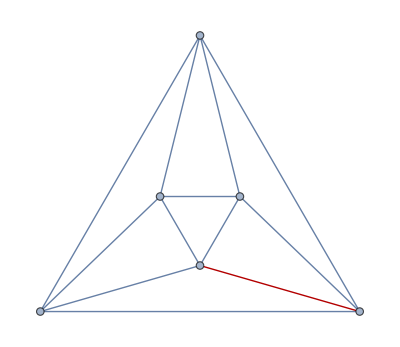
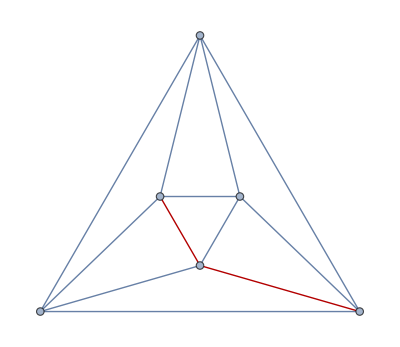
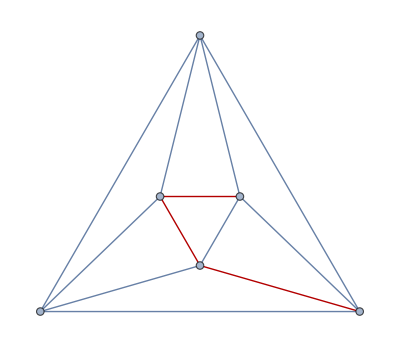
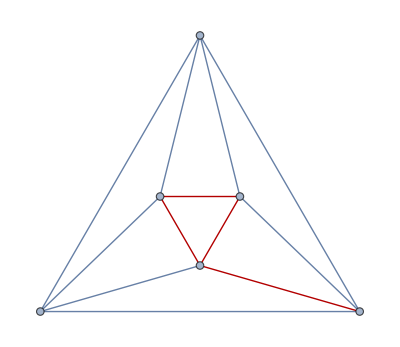
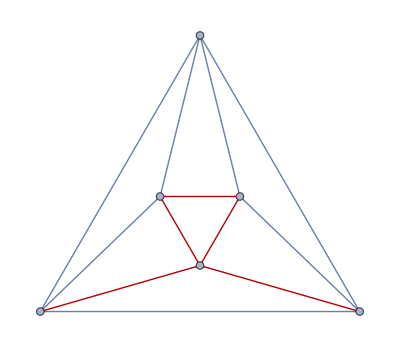
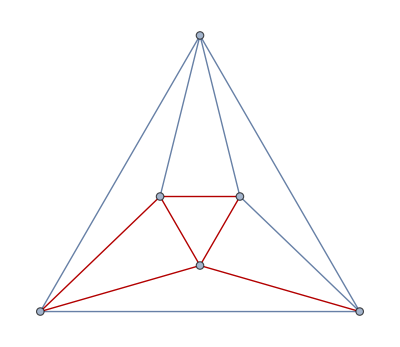
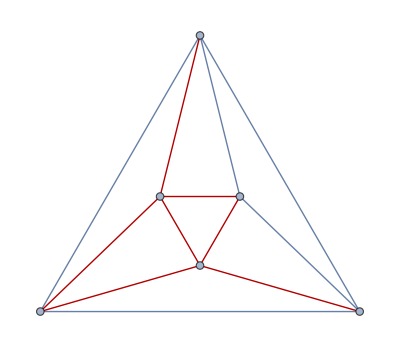
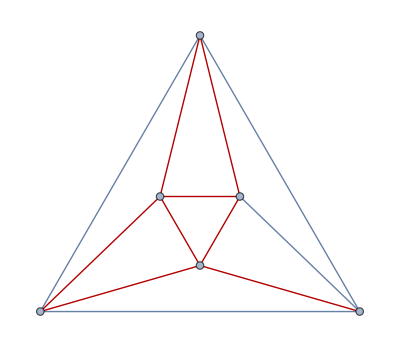

```mathematica
g=GraphData["OctahedralGraph"];
ec=FindEulerianCycle[g];
Table[HighlightGraph[g,Part[First[%],1;;i]],{i,Length[First[ec]]}]
```

```mathematica
Sum[StirlingS2[5,k],{k,1,5}]
```

52

```mathematica
BellB[5]
```

52

```mathematica
Map[{#,PrimeNu[#]}&,{210,60,36,24,16}]//tf
```

210 | 4
60 | 3
36 | 2
24 | 2
16 | 1

```mathematica
Table[Binomial[n,k],{n,0,6},{k,0,n}]//tf
```

1 |  |  |  |  |  | 
1 | 1 |  |  |  |  | 
1 | 2 | 1 |  |  |  | 
1 | 3 | 3 | 1 |  |  | 
1 | 4 | 6 | 4 | 1 |  | 
1 | 5 | 10 | 10 | 5 | 1 | 
1 | 6 | 15 | 20 | 15 | 6 | 1

```mathematica
Table[StirlingS2[n,k],{n,0,5},{k,0,n}]//tf
```

1 |  |  |  |  | 
0 | 1 |  |  |  | 
0 | 1 | 1 |  |  | 
0 | 1 | 3 | 1 |  | 
0 | 1 | 7 | 6 | 1 | 
0 | 1 | 15 | 25 | 10 | 1

```mathematica
nnFactorList[2730+1260]
```

{{3990},{2,1995},{6,665},{3,1330},{133,30},{15,266},{5,798},{10,399},{19,210},{38,105},{35,114},{57,70},{7,570},{14,285},{95,42},{21,190},{2,3,665},{2,15,133},{2,5,399},{2,19,105},{2,57,35},{2,7,285},{2,21,95},{5,6,133},{3,10,133},{3,5,266},{19,6,35},{3,19,70},{3,38,35},{7,6,95},{3,7,190},{3,14,95},{7,19,30},{19,14,15},{7,38,15},{5,19,42},{19,10,21},{5,38,21},{5,7,114},{7,10,57},{5,14,57},{2,3,5,133},{2,3,19,35},{2,3,7,95},{2,7,19,15},{2,5,19,21},{2,5,7,57},{5,7,19,6},{3,7,19,10},{3,5,19,14},{3,5,7,38},{2,3,5,7,19}}

```mathematica
i=2;
Table[{{k,i++}},{n,1,4},{k,n,1,-1}]//tf
```

1 | 2 |  |  | 
2 | 3 | 1 | 4 |  | 
3 | 5 | 2 | 6 | 1 | 7 | 
4 | 8 | 3 | 9 | 2 | 10 | 1 | 11

```mathematica
Array[{#1,#2^2}&,{2,3}]
```

{{{1,1},{1,4},{1,9}},{{2,1},{2,4},{2,9}}}